```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Markovian beta Data eta_non-zero"];
LNDatabeta001=ReadList["LNData_M_beta_0.01.txt"];
LNDatabeta002=ReadList["LNData_M_beta_0.02.txt"];
LNDatabeta003=ReadList["LNData_M_beta_0.03.txt"];
LNDatabeta004=ReadList["LNData_M_beta_0.04.txt"];
LNDatabeta005=ReadList["LNData_M_beta_0.05.txt"];
LNDatabeta006=ReadList["LNData_M_beta_0.06.txt"];
LNDatabeta012=ReadList["LNData_M_beta_0.12.txt"];
```

```mathematica
beta001=Table[Table[{LNDatabeta001[[pair]][[pt]][[1]], 0.01, LNDatabeta001[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta002=Table[Table[{LNDatabeta002[[pair]][[pt]][[1]], 0.02, LNDatabeta002[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta003=Table[Table[{LNDatabeta003[[pair]][[pt]][[1]], 0.03, LNDatabeta003[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta004=Table[Table[{LNDatabeta004[[pair]][[pt]][[1]], 0.04, LNDatabeta004[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta005=Table[Table[{LNDatabeta005[[pair]][[pt]][[1]], 0.05, LNDatabeta005[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta006=Table[Table[{LNDatabeta006[[pair]][[pt]][[1]], 0.06, LNDatabeta006[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta012=Table[Table[{LNDatabeta012[[pair]][[pt]][[1]], 0.12, LNDatabeta012[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
```

```mathematica
(* Modified Data Order: LN34, LN12, LN14=LN23, LN13=LN24*)
betaData={
{beta001[[6]], beta001[[1]], beta001[[3]],beta001[[2]]},
{beta002[[6]], beta002[[1]], beta002[[3]], beta002[[2]]},
{beta003[[6]], beta003[[1]], beta003[[3]],beta003[[2]]},
{beta004[[6]], beta004[[1]], beta004[[3]],beta004[[2]]},
{beta005[[6]], beta005[[1]], beta005[[3]],beta005[[2]]},
{beta006[[6]], beta006[[1]], beta006[[3]],beta006[[2]]},
{beta012[[6]], beta012[[1]], beta012[[3]],beta012[[2]]}};
```

```mathematica
PlotFormat={PlotRange->{{0, 500}, {0.01, 0.06}, {0, 3.1}}, Filling->Bottom, PlotStyle->{Directive[Red, Thickness[0.0020]], Directive[Lighter[Blue], Thickness[0.0020]], Directive[Darker[Green], Thickness[0.0020]], Directive[Yellow, Thickness[0.0030]]}, AxesLabel->{"τ", "β", "𝒩"}, LabelStyle->Directive[Black, FontSize->20, FontFamily->"Latin Modern Roman"], Ticks->{Table[time, {time, 0, 500, 100}], Table[beta, {beta, 0, 0.06, 0.01}], Automatic}, BoxRatios->{3.5, 3.5,0.7}};
ListLinePlot3D[betaData[[4]], Evaluate[PlotFormat]]
```

-Graphics3D-

```mathematica
betaplots=Table[ListLinePlot3D[betaData[[n]], Evaluate[PlotFormat]], {n, 1, 6}];
MarkovianSystemBeta=Show[betaplots, ImageSize->Large, ViewPoint->{2, -2.5, 2.5}]
```

-Graphics3D-

```mathematica
Export["Markovian System Beta.png",MarkovianSystemBeta]
```

Markovian System Beta.png

```mathematica
GetPeaks[Data_]:=Module[{Output},
Output={};
Table[If[Data[[pt]][[2]]>Data[[pt-5]][[2]]&&Data[[pt]][[2]]>Data[[pt+5]][[2]]&&Data[[pt]][[2]]>Data[[pt-4]][[2]]&&Data[[pt]][[2]]>Data[[pt+4]][[2]]&&Data[[pt]][[2]]>Data[[pt-3]][[2]]&&Data[[pt]][[2]]>Data[[pt+3]][[2]]&&Data[[pt]][[2]]>Data[[pt-2]][[2]]&&Data[[pt]][[2]]>Data[[pt+2]][[2]]&&Data[[pt]][[2]]>Data[[pt-1]][[2]]&&Data[[pt]][[2]]>Data[[pt+1]][[2]], AppendTo[Output, Data[[pt]]]], {pt, 6, Length[Data]-5}];
Return[Output];
]
PeakData=Sort[GetPeaks[Join[LNDatabeta002[[1]], LNDatabeta002[[6]]]]]
```

{{1.,2.93311},{6.,0.0666988},{19.5,0.0484387},{26.,2.76606},{31.,0.101016},{45.,0.0722719},{51.,2.49436},{56.5,0.16631},{67.5,0.153634},{76.5,2.17121},{84.5,0.259683},{92.5,0.284227},{104.,1.85269},{109.5,0.411714},{129.,1.55548},{134.5,0.512088},{137.5,0.483259},{154.5,1.26662},{162.5,0.645329},{187.5,0.714829},{187.5,1.25455},{215.,0.686081},{215.,1.34328},{226.,0.495257},{240.,0.672641},{240.,1.36123},{265.,1.23494},{265.5,0.532502},{292.5,1.05259},{293.,0.414536},{295.5,1.0765},{318.,0.245114},{323.5,1.25136},{346.,0.0796403},{351.,1.41865},{376.,1.58497},{401.,1.67058},{429.,1.73527},{454.,1.76527},{479.,1.66998}}

```mathematica
KeepPeaks2={{1.,2.93310791493926},{26.,2.7660648163091506},{51.,2.4943595499597713},{76.5,2.1712056126572796},{104.,1.8526874606038373},{129.,1.5554750316478003},{134.5,0.5120875735836415},{137.5,0.4832588441793414},{154.5,1.2666168540444551},{162.5,0.645329068359749},{187.5,Mean[{0.714828765246392,1.2545530705158767}]},{215.,Mean[{0.6860805700500019,1.3432840865786786}]},{226.,0.4952573774113217},{240.,Mean[{0.6726409111654754,1.3612313960934905}]},{265.,1.2349368641253078},{265.5,0.5325021422637084},{292.5,1.0525920090363363},{293.,0.41453632955034597},{295.5,1.0765019538674458},{318.,0.24511350256566447},{323.5,1.2513586593500297},{346.,0.07964028770758738},{351.,1.4186531721360853},{376.,1.584966098262923},{401.,1.6705834394633086},{429.,1.7352654750485685},{454.,1.7652747970286988},{479.,1.6699753012550618}};
KeepPeaks4={{1.,2.9196150353322836},{26.,2.4214722412565353},{51.5,2.0367021169098685},{76.5,1.65819835468313},{104.,1.373689575502738},{129.5,1.0809433064790175},{157.,0.8596905477840902},{160.,0.8950247596259915},{187.5,0.9598016891578133},{215.,0.9616321237334933},{240.,0.9555481977898551},{265.,0.8175076391311228},{293.,0.6987111909859971},{320.5,0.6671880013795191},{348.5,0.7442098126807151},{376.,0.8056373469769584},{401.,0.861557484596136},{429.,0.8484212085472891},{454.,0.86941077491249},{479.,0.7700527446857582},{482.,0.7401216763219759}};

EnvelopFunc2=Interpolation[KeepPeaks2];
EnvelopFunc4=Interpolation[KeepPeaks4];
```

```mathematica
(* Plot Formatting *)
Title="Markovian System: {n=4, β=0.04, η=0.07, m=1, ω=1, Ω=n/a, γ=n/a}"; 
height=400;
width=600;
PlotFormat={Joined->True, PlotRange->{0, 2.5}, ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black,20], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 20], PlotLabel->None, PlotStyle->{Thickness[0.0010]}};

(* Plot LN Data of the System *)
(* Data order should be LN34 (Red), LN12 (Blue), LN14=LN23 (Green), LN13=LN24 (Yellow) *)
LNPlot1=ListLinePlot[{LNDatabeta001[[6]][[800;;1001]], LNDatabeta001[[1]][[800;;1001]], LNDatabeta001[[3]][[800;;1001]], LNDatabeta001[[2]][[800;;1001]]}, PlotStyle->{Directive[Lighter[Red, 0.60], Thickness[0.0030]], Directive[Lighter[Blue, 0.60], Thickness[0.0030]], Directive[Darker[Green], Thickness[0.0030]], Directive[Yellow, Thickness[0.0030]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];
LNPlot2=ListLinePlot[{LNDatabeta002[[6]][[800;;1001]], LNDatabeta002[[1]][[800;;1001]], LNDatabeta002[[3]][[800;;1001]], LNDatabeta002[[2]][[800;;1001]]}, PlotStyle->{Directive[Lighter[Red, 0.45], Thickness[0.0030]], Directive[Lighter[Blue, 0.45], Thickness[0.0030]], Directive[Darker[Green], Thickness[0.0030]], Directive[Yellow, Thickness[0.0030]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];
LNPlot3=ListLinePlot[{LNDatabeta003[[6]][[800;;1001]], LNDatabeta003[[1]][[800;;1001]], LNDatabeta003[[3]][[800;;1001]], LNDatabeta003[[2]][[800;;1001]]}, PlotStyle->{Directive[Lighter[Red, 0.30], Thickness[0.0030]], Directive[Lighter[Blue, 0.30], Thickness[0.0030]], Directive[Darker[Green], Thickness[0.0030]], Directive[Yellow, Thickness[0.0030]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];
LNPlot4=ListLinePlot[{LNDatabeta004[[6]][[800;;1001]], LNDatabeta004[[1]][[800;;1001]], LNDatabeta004[[3]][[800;;1001]], LNDatabeta004[[2]][[800;;1001]]}, PlotStyle->{Directive[Lighter[Red, 0.15], Thickness[0.0030]], Directive[Lighter[Blue, 0.15], Thickness[0.0030]], Directive[Darker[Green], Thickness[0.0030]], Directive[Yellow, Thickness[0.0030]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];
LNPlot5=ListLinePlot[{LNDatabeta005[[6]][[800;;1001]], LNDatabeta005[[1]][[800;;1001]], LNDatabeta005[[3]][[800;;1001]], LNDatabeta005[[2]][[800;;1001]]}, PlotStyle->{Directive[Lighter[Red, 0.15], Thickness[0.0030]], Directive[Lighter[Blue, 0.15], Thickness[0.0030]], Directive[Darker[Green], Thickness[0.0030]], Directive[Yellow, Thickness[0.0030]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];
LNPlot6=ListLinePlot[{LNDatabeta006[[6]][[800;;1001]], LNDatabeta006[[1]][[800;;1001]], LNDatabeta006[[3]][[800;;1001]], LNDatabeta006[[2]][[800;;1001]]}, PlotStyle->{Directive[Lighter[Red, 0.90], Thickness[0.0030]], Directive[Lighter[Blue, 0.90], Thickness[0.0030]], Directive[Darker[Green], Thickness[0.0030]], Directive[Yellow, Thickness[0.0030]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];

(* Data order should be LN34 (Red), LN12 (Blue), LN14=LN23 (Green), LN13=LN24 (Yellow) *)
(* LNPLotwithEnvelopFunc2=Show[LNPlot4, Plot[EnvelopFunc2[x], {x, 1, 500}, PlotStyle->Directive[Dashed, Gray], PlotRange->All]]
LNPLotwithEnvelopFunc4=Show[LNPlot4, Plot[EnvelopFunc4[x], {x, 1, 500}, PlotStyle->Directive[Dashed, Gray], PlotRange->All]]*)
```

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian beta Data eta_non-zero no resonance"];
LNDatabeta003NM=ReadList["LNData_NM_beta_0.03.txt"];
LNDatabeta006NM=ReadList["LNData_NM_beta_0.06.txt"];
LNDatabeta009NM=ReadList["LNData_NM_beta_0.09.txt"];
LNDatabeta012NM=ReadList["LNData_NM_beta_0.12.txt"];

LNPlotNM003=ListLinePlot[{LNDatabeta003NM[[6]][[800;;1001]], LNDatabeta003NM[[1]][[800;;1001]], LNDatabeta003NM[[3]][[800;;1001]], LNDatabeta003NM[[2]][[800;;1001]]}, PlotStyle->{Directive[Magenta, Thickness[0.0040], Dashed], Directive[Cyan, Thickness[0.0040], Dashed], Directive[Green, Thickness[0.0040], Dashed], Directive[Orange, Thickness[0.0040], Dashed]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->None];
LNPlotNM006=ListLinePlot[{LNDatabeta006NM[[6]][[800;;1001]], LNDatabeta006NM[[1]][[800;;1001]], LNDatabeta006NM[[3]][[800;;1001]], LNDatabeta006NM[[2]][[800;;1001]]}, PlotStyle->{Directive[Magenta, Thickness[0.0040], Dashed], Directive[Cyan, Thickness[0.0040], Dashed], Directive[Green, Thickness[0.0040], Dashed], Directive[Orange, Thickness[0.0040], Dashed]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->None];
LNPlotNM009=ListLinePlot[{LNDatabeta009NM[[6]][[800;;1001]], LNDatabeta009NM[[1]][[800;;1001]], LNDatabeta009NM[[3]][[800;;1001]], LNDatabeta009NM[[2]][[800;;1001]]}, PlotStyle->{Directive[Magenta, Thickness[0.0040], Dashed], Directive[Cyan, Thickness[0.0040], Dashed], Directive[Green, Thickness[0.0040], Dashed], Directive[Orange, Thickness[0.0040], Dashed]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->None];
LNPlotNM012=ListLinePlot[{LNDatabeta012NM[[6]][[800;;1001]], LNDatabeta012NM[[1]][[800;;1001]], LNDatabeta012NM[[3]][[800;;1001]], LNDatabeta012NM[[2]][[800;;1001]]}, PlotStyle->{Directive[Magenta, Thickness[0.0040], Dashed], Directive[Cyan, Thickness[0.0040], Dashed], Directive[Green, Thickness[0.0040], Dashed], Directive[Orange, Thickness[0.0040], Dashed]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->None];
```

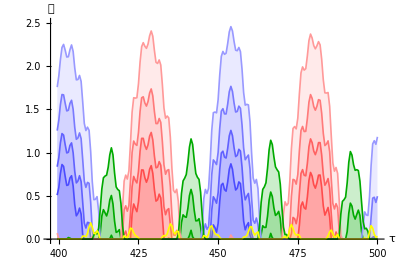
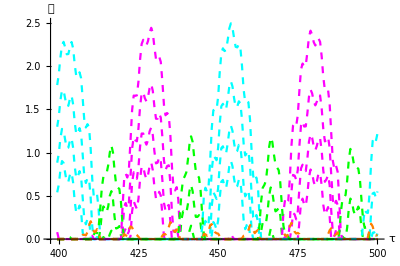

```mathematica
(* Markovian Beta = 0.02, and 0.04 *)  (* non-Markovian Beta = 0.06 and 0.12 *)
Row[{Show[{LNPlot4, LNPlot3,LNPlot2, LNPlot1}], Show[{LNPlotNM012, LNPlotNM009, LNPlotNM006, LNPlotNM003}]}]
```

```mathematica
NMcompareMBeta=Rasterize[Row[{Show[{LNPlot4, LNPlot3,LNPlot2, LNPlot1,LNPlotNM012, LNPlotNM009, LNPlotNM006, LNPlotNM003}]}]]
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Environmental Coupling beta and eta non-zero no Resonance"];
Export["non-Markovian and Markovian Beta Comparison.png", NMcompareMBeta]
```

non-Markovian and Markovian Beta Comparison.png